semelparous

```mathematica
ClearAll["Global`*"]
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, μr,b,σ,ρ,ϕ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]},  
{s,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μr, b,σ,ρ,ϕ,n]=First@Evaluate[(σ (s[T]+ϕ r[T])/(1+ρ (s[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, μr_, b_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[vr[t], t]==γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr] -δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm] -δ vm[t]-β s[t]*vm[t],
D[r[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr]+β Exp[-τm μ]*s[t-τm]*vm[t-τm] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]
```

very low host fecundity (ϕ = 0.1) - figures in the main text use 0.5

```mathematica
Clear[v0,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,0.25,75, 200,0.0001,0.1,#]&/@Range[500];
seq1000=Union[seq[[400;;500]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.2,0.01}],1];
```

```mathematica
(*Export["nonokp_sc.mx",all]*)
```

```mathematica
all=Import["nonokp_sc.mx"];
```

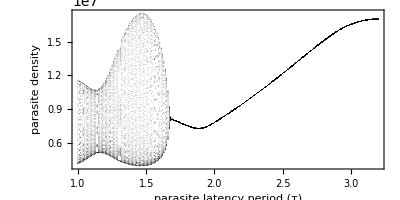

```mathematica
Graphics[{PointSize[0.001],Opacity[0.4],Point[all]},AspectRatio->1/2,Frame->True,FrameStyle->14,FrameLabel->{"parasite latency period (τ)","parasite density","ϕ = 0.1"}]
```

```mathematica
Clear[v0,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,10,75, 200,0.0001,0.1,#]&/@Range[500];
seq1000=Union[seq[[400;;500]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.2,0.01}],1];
```

```mathematica
(*Export["nonokp_scm.mx",all]*)
```

```mathematica
all=Import["nonokp_scm.mx"];
```

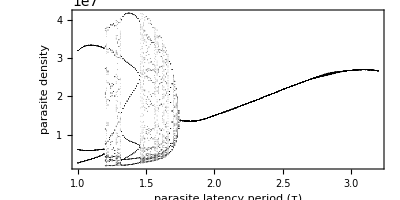

```mathematica
Graphics[{PointSize[0.001],Opacity[0.4],Point[all]},AspectRatio->1/2,Frame->True,FrameStyle->14,FrameLabel->{"parasite latency period (τ)","parasite density","μ_r = 10"}]
```

```mathematica
Clear[v0,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,5,75, 200,0.0001,0.1,#]&/@Range[500];
seq1000=Union[seq[[400;;500]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.2,0.01}],1];
```

```mathematica
(*Export["nonokp_scm2.mx",all]*)
```

```mathematica
all=Import["nonokp_scm2.mx"];
```

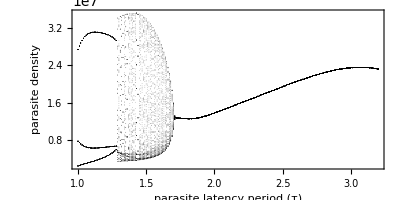

```mathematica
Graphics[{PointSize[0.001],Opacity[0.4],Point[all]},AspectRatio->1/2,Frame->True,FrameStyle->14,FrameLabel->{"parasite latency period (τ)","parasite density","μ_r = 5"}]
```

```mathematica
Clear[v0,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,#]&/@Range[500];
seq1000=Union[seq[[400;;500]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.2,0.01}],1];
```

iteroparous

```mathematica
ClearAll["Global`*"]
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
ωx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ,μi, μr,b,σ,ρ,ϕ,γ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]},  
{s,i,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,n]=First@Evaluate[(σ (s[T]+ϕ i[T]+ ϕ r[T])/(1+ρ (s[T]+i[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_,μi_, μr_, b_,γ_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0 j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[ir[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr] -ir[t](μi +γ),
D[im[t], t]==β Exp[-τm μ]*s[t-τm]*vm[t-τm] -im[t](μi +γ),
D[r[t], t]==γ (ir[t]+im[t])-μr r[t],
D[vr[t], t]==ωx[τr,b] *ir[t]-δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==ωx[τm,b] *im[t]-δ vm[t]-β s[t]*vm[t],
s[t/;t≤0]==0,ir[t/;t≤0]==0,im[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]
```

very low host fecundity (ϕ = 0.1) - figures in the main text use 0.5

```mathematica
Clear[v0,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.1,3,#]&/@Range[500];
seq1000=Union[seq[[400;;500]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.2,0.01}],1];
```

```mathematica
(*Export["nonokp_ic.mx",all]*)
```

```mathematica
all=Import["nonokp_ic.mx"];
```

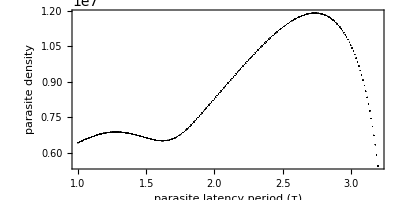

```mathematica
Graphics[{PointSize[0.001],Opacity[0.4],Point[all]},AspectRatio->1/2,Frame->True,FrameStyle->14,FrameLabel->{"parasite latency period (τ)","parasite density","ϕ = 0.1"}]
```

```mathematica
Clear[v0,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,5,5,200, 200,0.0001,0.5,3,#]&/@Range[500];
seq1000=Union[seq[[400;;500]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.2,0.01}],1];
```

```mathematica
(*Export["nonokp_icm.mx",all]*)
```

```mathematica
all=Import["nonokp_icm.mx"];
```

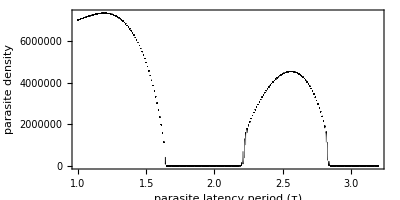

```mathematica
Graphics[{PointSize[0.001],Opacity[0.4],Point[all]},AspectRatio->1/2,Frame->True,FrameStyle->14,FrameLabel->{"parasite latency period (τ)","parasite density","μ_r, μ_i = 5"}]
```